```mathematica
Get["DMTestFunctions`"]
Get["DifferenceMapOptimizer`"]
Get["DMData`"]
Get["DMUtils`"]
```

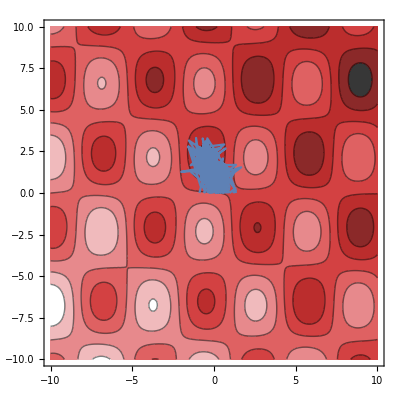
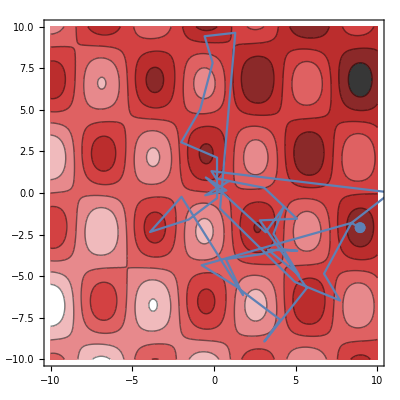
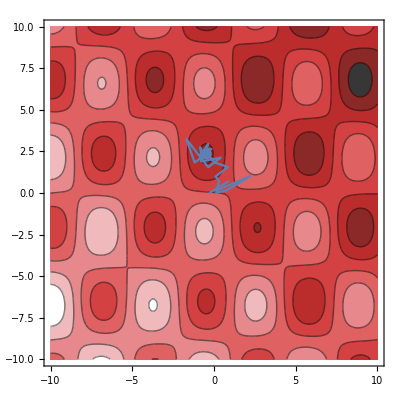
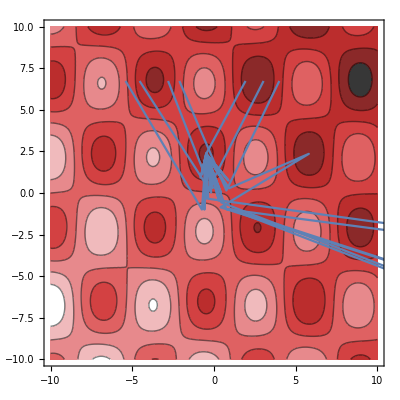
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Automatic | {SimulatedAnnealing,PerturbationScale→5.} | DifferentialEvolution | NelderMead | RandomSearch

```mathematica
builtinMethods = {Automatic, {"SimulatedAnnealing", "PerturbationScale" -> 5.0}, "DifferentialEvolution", "NelderMead", "RandomSearch"};
vars = {x, y};
offset = {100, 100};
range = Sequence[{x, -10, 10}, {y, -10, 10}];
nicePlot[method_] := Module[{fun, solution, minima},
{{fun, solution}, {minima}} =
Reap[
NMinimize[
griewankN[vars - offset],
vars, 
EvaluationMonitor-> Hold[Sow[vars]], 
Method->method, 
MaxIterations->100]
];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True], 
ListPlot[{Map[# /. solution &, vars]}]
]
];
Grid[{Map[nicePlot, builtinMethods], builtinMethods}]
```

```mathematica
(* Create a plot of the griewank function with the three initial points (x_0, x_0^*, and x_1) overlayed (hard to see.) *)
start = {4, 7};
other = {7, 8};
fun = N[griewankN[start]];
{fun2, solution} = FindMinimum[griewankN[{x, y}], {x, 4}, {y, 7}];
sol = {x, y} /. solution
Show[Plot3D[griewankN[{x, y}], {x, -10, 10}, {y, -10, 10}], ListPointPlot3D[{Join[start, {fun+0.01}],  Join[sol, {fun2+0.02}], Append[other, griewankN[other]]}]]
```

{3.14002,4.43844}

```mathematica
Plus @@ <|
"d" -> 1,
"e" -> 5
|>
```

6

```mathematica
(* EXPERIMENT *)
With[{
dim = 4,
maxnfev = 20000,
innerNiter = 65,
secondPointDistance = 5,
prelimRunCount = 10,
prelimNiter = 5
},
Module[{preliminaryResults, nfevsPerIter},
(* Collect preliminary results to estimate how many function evaluations are needed per iteration for each solver. With this information, we can then estimate how many iterations to run each solver for, on top of using a random restart strategy (implemented in DMData.m). *)
preliminaryResults = ToAssociations[
makeResults[
<|
"dim" -> dim,
"niter" -> prelimNiter,
"runCount" -> prelimRunCount,
"innerNiter" -> innerNiter,
"secondPointDistance" -> secondPointDistance,
"tolerance" -> 1 10^-8,
"randomrestart" -> False,
"maxnfev" -> 1,
"solversToDo" -> {"sa", "de", "nm", "rs", "dm"} (* all the solvers *)
|>
]
];
Print["Computing statistics."];
preliminaryResults = Map[
Function[solverData,
N @* Plus @@ Map[
Function[functionData,
Plus @@ Map[#[["nfev"]] &, functionData] / prelimRunCount
],
solverData
] / Length[solverData]
],
preliminaryResults
] / prelimNiter
]
]
```

### Solver: dm

### Solver: de

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 5 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

### Solver: sa

### Solver: nm

### Solver: rs

Computing statistics.

<|dm→279.888,de→89.28,sa→59.32,nm→46.36,rs→1834.6|>

```mathematica
builtinResults = ToAssociations[
makeResults[
<|
"dim" -> 4,
"niter" -> 100,
"runCount" -> 10,
"innerNiter" -> 65,
"secondPointDistance" -> 5,
"maxnfev" -> 14000,
"solversToDo" -> {"sa", "de", "nm", "rs"}
|>
]
];
```

```mathematica
builtinResults[["sa", "griewank", 1, "fun"]]
```

0.184822

```mathematica
builtinResults
```

<|sa→<|griewank→{1},3,ackley→{<|fun→15.3004,x→{-4.99394,3},nfev→1,iterate→{{19.2651,22.0438,11.0937,29.9648},{2.67236,-2.0398,29.936,-3.88149},90,{-4.99394,-3.99515,-4.74188×10^-9,12.9842}}|>,<|1|>,<|1|>}|>|>
 |  |  |  |

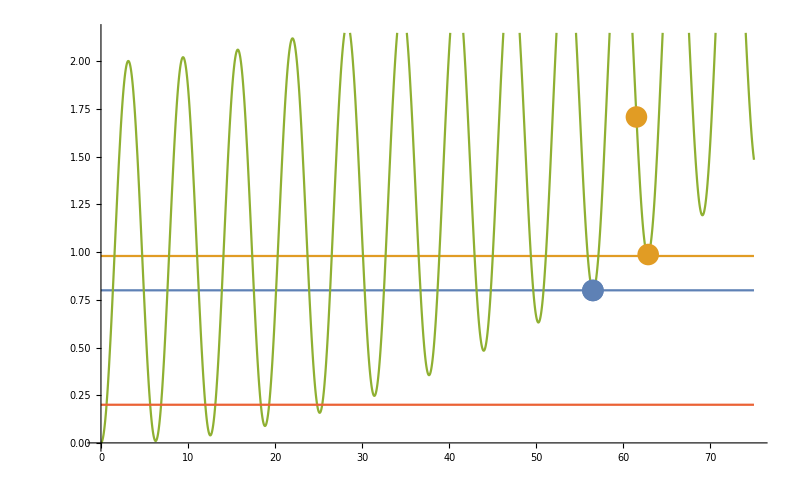

```mathematica
Show[
Plot[{0.8, 0.98, griewankN @ {xi}, 0.2}, {xi, 0, 75}],
ListPlot[{{{56.5, griewankN @ {56.5}}}, {{61.5, griewankN @ {61.5}}, {62.85, griewankN @ {62.85}}}}]
]
```